```mathematica
<< WorldPlot`
```

```mathematica
rawdata=Import[ToFileName[NotebookDirectory[],"data.csv"],"CSV"];
```

```mathematica
data=Rest[rawdata];
```

```mathematica
rawdata[[1]]
```

{Number,Name,Country,Lat,Long,Height,Jan,Feb,Mar,Apr,May,Jun,Jul,Aug,Sep,Oct,Nov,Dec}

```mathematica
coords=data[[All,4;;5]];
```

```mathematica
wm=WorldPlot[{World,RandomGrays}];
```

```mathematica
mcoords = Map[{ToMinutes[#[[1]]],-1*ToMinutes[#[[2]]]}&,coords,{1}] ;
```

```mathematica
wg=WorldGraphics[Join[{Red},Point /@ mcoords]];
```

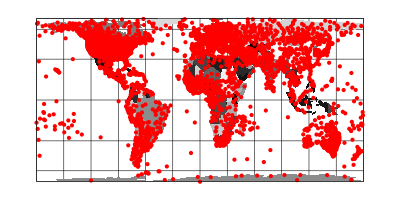

```mathematica
Show[{wm,wg},WorldProjection->LambertCylindrical]
```